#### 1. Legalább két módszerrel generáljuk ki egy listába az kettő hatványok közül az első húszat (konkrétan a következőket: 2^1,2^2,...,2^20), majd ábrázoljuk őket (az egyik módszernél használjuk a ListPlot parancsot, a másiknál a ListLinePlot-ot).

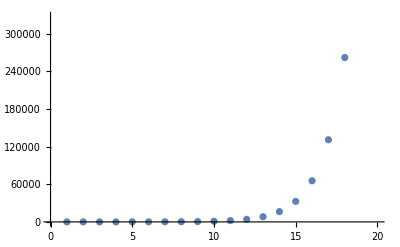

```mathematica
ListPlot[Table[2^i, {i, 20}]]
```

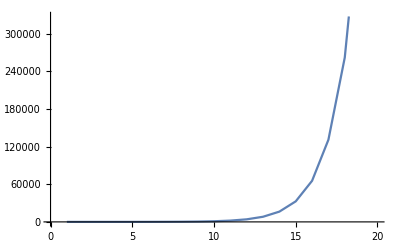

```mathematica
ListLinePlot[(2^#&)/@Range[20]]
```

#### 2. Egy ferdén elhajított test helyzetének koordinátáit a t. időpillanatban az x=v_0·cos(φ)·t y=y_0+v_0·sin(φ)·t-5 t^2 rendszer adja. Rajzoljuk ki az első négy másodpercben megtett pályát. A v_0, φ,y_0 és paramétereket egy Manipulate ablak segítségével adjuk meg.

```mathematica
Manipulate[ParametricPlot[{v*Cos[alpha]*t, y + v*Sin[alpha]*t-5*t^2}, {t, 0, 4}],{v, 0, 10}, {alpha, 0, 2Pi}, {y, 0, 10}]
```

#### 3. Animáljunk egy propellert (két egymásra merőleges szakaszt, ami óra mutatójárásával ellentétes irányban forog). Tipp : lehet használni a beépített Rotate függvényt. Ha nem sikerül szépre az animáció tanulmányozzuk a RefreshRate, AnimationRate opciókat.

```mathematica
line1 = Line[{{-1, 0}, {1, 0}}];
line2 = Rotate[line1, -Pi/2];
prop = Graphics[{line1, line2}]
(*Animate[prop, {a, -1, 0}, {b, 1, 0}]*)
```

-Graphics-